{r∈Reals,r≥0}

4/(3 r^3)

2

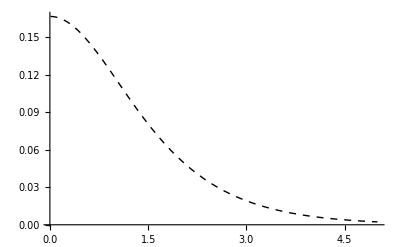

behaviour_integrand.pdf

```mathematica
ClearAll["Global`*"];
$Assumptions={r∈Reals, r≥0}
Limit[1/x*Exp[x]/(Exp[x]-1)^2*(π - (2 r/x)/((r/x)^2+1)-2ArcTan[r/x]),x->0]
r=2
Plot[1/x*Exp[x]/(Exp[x]-1)^2*(π - (2 r/x)/((r/x)^2+1)-2ArcTan[r/x]),{x,0.01,5},PlotRange->All,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Dashed,Thick}}]
Export["behaviour_integrand.pdf",%]
```

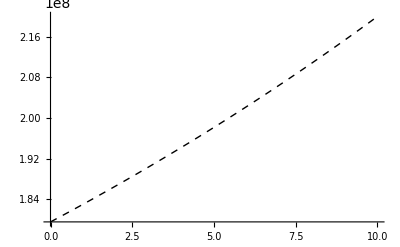

```mathematica
ClearAll["Global`*"];
$Assumptions={x∈Reals,x≥0,r≥0};
f1[x_]:=Exp[x]/(x*(Exp[x]-1)^2)
f2[x_]:=(π-((2*r)/x)/(1+(r/x)^2)-2ArcTan[r/x])
f3[r_,x_]:=1/x^3*(π-((2*r)/x)/(1+(r/x)^2)-2ArcTan[r/x])
Plot[(f3[r,x])^(-3/2)/.{x->100},{r,0.001,10},PlotRange->All,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Dashed,Thick}}]
(*Export["dependence_integrand.pdf",%]*)
```

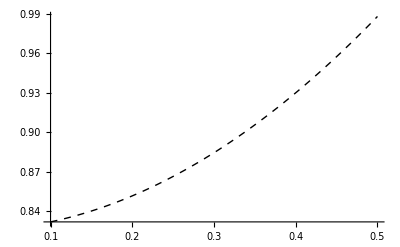

```mathematica
ClearAll["Global`*"];
$Assumptions={x∈Reals,x≥0,r≥0};
f1[x_]:=Exp[x]/(x*(Exp[x]-1)^2)
f2[x_]:=(π-((2*r)/x)/(1+(r/x)^2)-2ArcTan[r/x])
f3[r_,x_]:=1/x^3*(π-((2*r)/x)/(1+(r/x)^2)-2ArcTan[r/x])
Plot[(f3[r,x])^(-2/3)/.{r->1},{x,0.1,0.5},PlotRange->All,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Dashed,Thick}}]
```

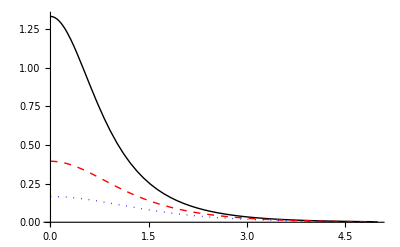

x-dependence.pdf

```mathematica
listofplots1=Table[f1[x]*f2[x],{r,{1,1.5,2}}];
plot1=Plot[listofplots1,{x,0.001,5},PlotRange->All,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Thick},{Red,Dashed,Thick},{Blue,Dotted,Thick}}]
(*Export["x-dependence.pdf",%]*)
```

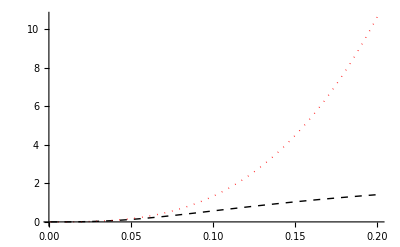

original_vs_approx1.pdf

```mathematica
taylorexpansion=Normal[Series[f2[x],{x,0,3}]];
plot2=Plot[Evaluate[{f2[x],taylorexpansion}/.{r->0.1}],{x,0.001,0.2},PlotRange->All,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Dashed,Thick},{Red,Dotted,Thick}}]
(*Export["original_vs_approx1.pdf",%]*)
```

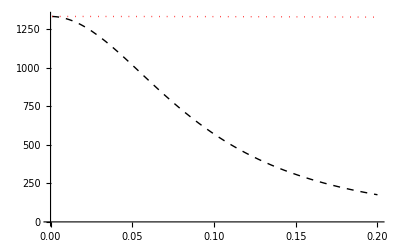

original_vs_approx2.pdf

```mathematica
plot3=Plot[Evaluate[{f1[x]*f2[x],f1[x]*taylorexpansion}/.{r->0.1}],{x,0.001,0.2},PlotRange->Automatic,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Dashed,Thick},{Red,Dotted,Thick}}]
(*Export["original_vs_approx2.pdf",%]*)
```

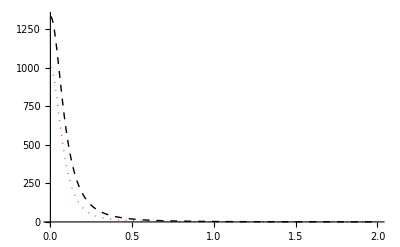

```mathematica
powercount[x_] := 1/((r^2+x^2)^(3/2))
plot4=Plot[Evaluate[{f3[0.1,x],powercount[x]}/.{r->0.1}],{x,0.001,2},PlotRange->All,AxesStyle->Arrowheads[{0,0.03}],PlotStyle->{{Black,Dashed,Thick},{Red,Dotted,Thick}}]
(*Export["original_vs_powercounting.pdf",%]*)
```

```mathematica
ClearAll["Global`*"];
$Assumptions={x∈Reals,x≥0,r≥0};
f1[x_]:=Exp[x]/(x*(Exp[x]-1)^2)
f2[x_]:=(π-((2*r)/x)/(1+(r/x)^2)-2ArcTan[r/x])
Integrate[f1[x]*f2[x],{x,r,∞}]
```

∫_r^∞ (ⅇ^x (π-(2 r)/((1+r^2/x^2) x)-2 ArcTan[r/x]))/((-1+ⅇ^x)^2 x)ⅆx